```mathematica
obbFormat[obb_] := Module[{p, dir, center, o, hw},
p = obb[[1]];
dir = obb[[2]];
center = p + 1/2{1,1,1}.dir;
o = Transpose[Normalize /@ dir];
hw = 1/2 Norm /@ dir;
Flatten[{center, o, hw}]
]
SetDirectory[NotebookDirectory[]];
n = 50;
tris = Table[Triangle[RandomReal[{-1, 1}, {3, 3}]], {i ,1, n}];
Export["tris.txt", Flatten /@ tris[[All, 1]], "Table"];
Graphics3D[tris]
spheres = Table[Ball[RandomReal[{-1, 1}, 3], RandomReal[{0.1, 0.5}]], {i ,1, n}];
Export["spheres.txt", {#[[1, 1]], #[[1,2]],#[[1,3]],#[[2]]} & /@ spheres, "Table"];
Graphics3D[spheres]
aabbs = Table[BoundingRegion[RandomReal[{-1, 1}, {3, 3}], "MinCuboid"], {i ,1, n}];
Export["aabbs.txt", Flatten[{#[[1]], #[[2]]}] & /@ aabbs, "Table"];
Graphics3D[aabbs]
obbs = Table[BoundingRegion[RandomReal[{-1, 1}, {4, 3}], "MinOrientedCuboid"], {i ,1, n}];
Export["obbs.txt", obbFormat/@ obbs, "Table"];
Graphics3D[obbs]
names = {"tri", "sphere", "aabb", "obb"};
primitives = {tris, spheres, aabbs, obbs};
Do[
results = Flatten[Table[If[RegionDisjoint[S, T], 0, 1], {S, primitives[[i]]}, {T, primitives[[j]]}]];
Export[names[[i]] <> "_" <> names[[j]] <> ".txt", Join[{n*n}, results], "Table"];
,
{i, 1, 4},
{j, 1, 4}
]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
spheres[[1]] /. Sphere->Ball
```

Ball[{0.924968,0.256526,-0.0726259},0.402161]

```mathematica
RegionDisjoint[spheres[[41]]/. Sphere->Ball, spheres[[50]]/. Sphere->Ball]
```

False

```mathematica
Sphere
```

```mathematica
Region
```

```mathematica
Graphics3D[{
Opacity[0.5],
spheres[[41]],
spheres[[50]]
}]
```

-Graphics3D-

```mathematica
obbFormat[[
```

```mathematica
Table[If[RegionDisjoint[S, T], 0, 1], {S, aabbs}, {T, obbs}]
```

{{1,1,1,1,1,1,1,1,0,1},{1,1,1,1,1,1,0,1,0,1},{0,1,1,1,1,1,1,1,0,1},{1,0,1,1,1,1,1,0,0,1},{1,1,1,1,1,1,1,1,0,1},{0,0,1,1,1,1,0,1,0,1},{1,1,1,1,1,1,1,1,0,1},{0,1,1,1,1,1,1,1,0,1},{0,0,1,0,0,1,0,0,1,1},{1,1,1,1,1,1,1,1,0,1}}

```mathematica
Graphics3D[{aabbs[[9]], obbs[[8]]}]
```

-Graphics3D-

```mathematica
RegionIntersection[aabbs[[2]], obbs[[7]]]
```

EmptyRegion[3]

```mathematica
RegionDisjoint[aabbs[[2]], obbs[[7]]]
```

True

```mathematica
aabbs[[2]]
```

Cuboid[{-0.253226,-0.946121,-0.510599},{0.876944,0.602521,0.77695}]

```mathematica
obbs[[2]]
```

Parallelepiped[{0.365644,-0.0486259,-0.203356},{{-0.776024,0.812588,-0.652099},{-1.27208,-0.585886,0.78375},{0.00575058,0.0324469,0.033589}}]

```mathematica
corners = ({{0, 0, 0}, {0, 0, 1}, {0, 1, 0}, {0, 1, 1}, {1, 0, 0}, {1, 0, 1}, {1, 1, 0}, {1, 1, 1}});
```

```mathematica
biunit = (2# - {1,1,1}) & /@ corners;
```

```mathematica
rangeAABB[aabb_, n_] := Module[{
c = 1/2(aabb[[1]] + aabb[[2]]).n,
R = 1/2(Abs /@ n).(aabb[[2]] - aabb[[1]])
},
{c - R, c + R}
]

rangeOBB[obb_, n_] := Module[{
values =(#.obb[[2]] + obb[[1]]).n & /@ corners
},
{Min[values], Max[values]}
]
```

```mathematica
rangeOBB2[obb_, n_] := Module[{p, dir, center, o, hw, r, c},
p = obbs[[2, 1]];
dir = obbs[[2, 2]];
center = p + 1/2{1,1,1}.dir;
o = Transpose[Normalize /@ dir];
hw = 1/2 Norm /@ dir;
c= center.n;
r = (Abs /@ (n.o)).hw;
{c - r, c + r}
]
```

```mathematica
s = 0;
t = 9;
c =  1/2(aabbs[[s+1, 1]] + aabbs[[s+1, 2]]);
p = spheres[[t+1, 1]];

q = RegionNearest[aabbs[[s+1]], p]
Norm[p - q]

Graphics3D[{
Opacity[0.5],
aabbs[[s + 1]],
spheres[[t+1]],
Line[{p, q}]
}]
```

{0.225655,-0.769821,0.147334}

0.

-Graphics3D-

```mathematica
Norm[ p-q]
```

0.565806

```mathematica
pts = tris[[1, 1]];
c = spheres[[10, 1]];
r = spheres[[10, 2]];
```

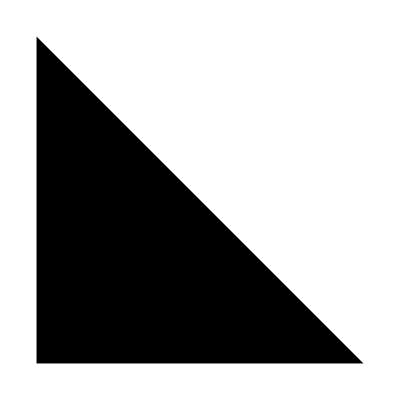

```mathematica
reg = Region[Triangle[{{0, 0}, {0, 1}, {1,0 }}]]
```

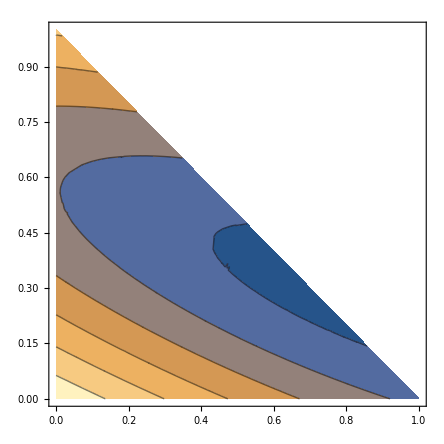

```mathematica
ContourPlot[Norm[c - pts.{u, v, 1 - u - v}], {u, v} ∈ reg]
```

```mathematica
p = RandomReal[{0, 1}, 2];
tri = {{0, 0}, RandomReal[{0, 1}, 2], RandomReal[{0, 1}, 2]}
```

{{0,0},{0.422665,0.817425},{0.935481,0.0855067}}

```mathematica
wuv[tri_, p_] := Module[{u, v},
{u, v} = LinearSolve[Transpose[{tri[[2]] - tri[[1]], tri[[3]] - tri[[1]]}], p - tri[[1]]];
{ 1 - u - v, u, v}
]
```

```mathematica
wuv[tri, p].tri
```

{0.898655,0.40147}

```mathematica
pWUV = wuv[tri, p];
```

```mathematica
pWUV
```

{-0.185407,0.410031,0.775376}

```mathematica
δ = wuv[tri, p] - {1/3,1/3,1/3}
δMax = Max[Abs[δ]]
```

{-0.51874,0.0766978,0.442042}

```mathematica
0.5187399968028283
```

0.51874

```mathematica
q ={1/3,1/3,1/3} + δ/(3δMax)
```

{0.,0.382618,0.617382}

```mathematica
Graphics[{
Opacity[0.25],
Triangle[tri],
Opacity[1.0],
Red,
Point[p],
Table[Circle[p, radius], {radius, 0, 0.4, 0.1}],
Blue,
Point[{1/3,1/3,1/3}.tri],
Point[q.tri]
}]
```

-Graphics-

```mathematica
pWUV
```

{-0.185407,0.410031,0.775376}

```mathematica
q
```

{0.,0.382618,0.617382}

```mathematica
δ
```

{-0.51874,0.0766978,0.442042}

```mathematica
p  = spheres[[10, 1]];
corners = tris[[2, 1]];
n = Normalize[Cross[corners[[2]] - corners[[1]], corners[[3]] - corners[[1]]]];
q = RegionNearest[tris[[2]],p]
```

{-0.0433786,-0.551362,-0.117736}

```mathematica
(p - corners[[1]]).n
```

-0.0866585

```mathematica
LinearSolve[Transpose[{corners[[2]] - corners[[1]], corners[[3]] - corners[[1]], n}], p - corners[[1]]]
```

{-0.515271,0.561476,-0.0866585}

```mathematica
corners = tris[[2, 1]];
```

```mathematica
LinearSolve[Transpose[tris[[2, 1]]], p]
```

{1.6648,-0.31069,0.678619}

```mathematica
Graphics3D[{
Opacity[0.5],
tris[[4]],
obbs[[3]]
}]
```

-Graphics3D-

```mathematica
dir= (corners[[2]] - corners[[1]]);
Norm[p -corners[[1]] - Max[0.0, Min[1.0,(dir.(p - corners[[1]]))/(dir.dir)]] dir]
```

0.715827

```mathematica
dir= (corners[[2]] - corners[[1]]);
Norm[corners[[1]] + Max[0.0, Min[1.0,(dir.(p - corners[[1]]))/(dir.dir)]] dir - p]
```

0.715827

```mathematica
RegionNearest[Line[{corners[[1]], corners[[2]]}], p]
```

{-0.281489,-0.321072,0.379366}

```mathematica
Norm[RegionNearest[Line[{corners[[1]], corners[[2]]}], p] - p]
Norm[RegionNearest[Line[{corners[[2]], corners[[3]]}], p] - p]
Norm[RegionNearest[Line[{corners[[3]], corners[[1]]}], p] - p]
```

0.783831

0.623283

0.436309

```mathematica
corners
```

{{0.185585,0.0122926,0.114415},{-0.182538,0.463142,-0.479178},{-0.20633,-0.952511,-0.282957}}

```mathematica
corners[[2]] - corners[[1]]
```

{-0.368123,0.45085,-0.593594}

```mathematica
p
```

{0.225655,-0.769821,0.147334}

```mathematica
names = {"Sam", "Cambro", "Cody", "DJ"};
RandomSample[names, 2]
```

{Cambro,Sam}

```mathematica
RandomSample[{"red", "blue"}, 1]
```

{red}

```mathematica
RandomSample[{"player", "spymaster"}, 1]
```

{player}